# Mathematica Tutorial 5

## Differential Equations

Warm-up: From classical mechanics, you’re well-aware of the coupled harmonic oscillator problem. The free-body diagram is shown below. Write down the (coupled!) equations of motion for both blocks.

```mathematica
?DSolve
```

Simple examples:

```mathematica
solution = DSolve[y'[x]==x,y[x],x]
```

As with solving any other equation, we can implement our solution as a replacement rule, i.e.

```mathematica
f[x_]:=Evaluate[y[x]/.solution[[1]]]
```

Then,

```mathematica
f[0]
f[2]
f[4]
```

## Exercise: Coupled Harmonic Oscillators

Consider the classical problem of two masses, connected by springs:

Exercise: Using the equations of motion, and the DSolve command, solve for x_1(t) and x_2(t). 
Assume that m_1=m_2, k_1≠k_2, and use the boundary conditions: x_1(0) = -2,x_1'(0) = 0, x_2(0) = 1, x_2'(0) = 0.

### Hint

We know that via Newton’s Second Law, we get two equations of motion:

F_1=-k_1 x_1-k_2(x_1-x_2)-m g
F_2=-k_2 (x_2-x_1)-m g

### Solution

```mathematica
DSolve[
{m x1''[t]==-k1 x1[t]-k2(x1[t]-x2[t])-m g,
m x2''[t]==-k2(x2[t]-x1[t])-m g,
x1[0]==-2, x1'[0]==0, x2[0]==1, x2'[0]==0}, 
{x1[t], x2[t]}, t];
%//FullSimplify
```

This may take a while. So let’s try and simplify the problem. As we’ve learned before, numerically solving something is almost always faster than analytically solving. So, take a look at NDSolve.

```mathematica
(*Why don't you type ?NDSolve into your computer, since mine is busy. Then use the Syntax given to solve the same ODE*)
```

### Numerical Solutions

Oh right, to use NDSolve, we’ll have to assign some numbers. Let’s take m = 1 kg, k_1 = 6 N/m, k_2 = 4 N/m, and g = 9.8 m/s^2

```mathematica
{m x1''[t]==-k1 x1[t]-k2(x1[t]-x2[t])-m g,
m x2''[t]==-k2(x2[t]-x1[t])-m g}/.{k1-> 6,k2-> 4, m-> 1,g->9.8}
{%, {x1[0]==-2, x1'[0]==0, x2[0]==1, x2'[0]==0}}
NDSolve[%, {x1[t], x2[t]}, {t, 0, 10}]
Plot[Evaluate[{x1[t],x2[t]}/.%[[1]]], {t, 0, 10},PlotLabel->"Trajectories of Coupled Spring System",PlotLegends->{"Mass 1","Mass 2"}]
```

## Problem: Quantum Harmonic Oscillator (Even Solutions)

Recall that the time-independent Schroedinger equation in 1D can be rewritten as an ODE:

(d^2 ψ)/dξ^2=(ξ^2-k)ψ

Define a procedure that solves the differential equation numerically for an input of the eigenvalue k. We are assuming an even solution (derivative zero at x = 0).The arbitrary condition that the solution is 1 at x = 0 has no physical implications.

#### Solution

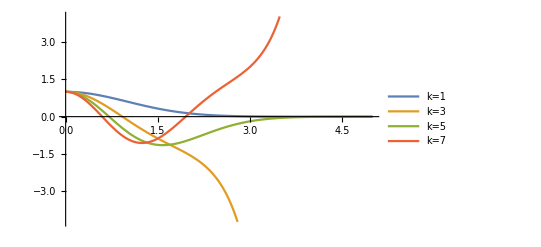

```mathematica
(*Solve the ODE for the appropriate boundary conditions *)
rule[k_]:=NDSolve[{u''[x]-(x^2-k)*u[x]==0,u[0]==1,u'[0]==0},u[x],{x,0,10}]
(*Apply that replacement rule (depending on k) and store result in a function (depending on x and k)*)
sol[k_,x_]:=u[x]/.rule[k][[1]]
(*Make a list of solutions for k values in {1,3,5,7} *)
listSol[x_]:=Table[sol[k,x],{k,1,7,2}]
(*Plot the list*)
Plot[Evaluate[listSol[x]],{x,0,5},PlotLegends->{"k=1","k=3","k=5","k=7"}]
```

Or, combined in a single function

```mathematica
(*Function to plot ODE solution given a value of k*)
ψ[k_]:=Plot[Evaluate[u[x]/.NDSolve[{u''[x]-(x^2-k)*u[x]==0,u[0]==1,u'[0]==0},u[x],{x,0,10}]],{x,0,5},PlotRange->{-10,10},PlotLabel->StringJoin["k=",ToString[k]]]
(*Table plotting range of k values*)
Table[ψ[n],{n,1,7,2}]
```

### Exercise: Quantum Harmonic Oscillator

Using the differential equation defining the quantum harmonic oscillator:

u''(x)-(x^2-k) u(x)==0

with the initial conditions

```mathematica
u'(0)==1
```

```mathematica
u(0)==0
```

create a module or define a function to plot odd solutions u(x), given an eigenvalue k. Plot for k=1, 3, 7. 

For each eigenvalue plot, plot graphs for k+\- 0.1, and comment on the normalizability of the solutions (i.e. why can we only get solutions to the wave equation for integer values of k?).

Reminder: Include name in Mathematica notebook, with a filename lastnamefirstinitial_Tutorial5.nb (eg. HoJ_Tutorial5.nb) and email the completed notebook to j.ho@example.ca

#### Solution

```mathematica
ψ[k_]:=Module[{},Plot[Evaluate[u[x]/.NDSolve[{u''[x]-(x^2-k)*u[x]==0,u[0]==0,u'[0]==1},u[x],{x,0,10}]],{x,0,5},PlotRange->{-10,10},PlotLabel->StringJoin["k=",ToString[k]]]]
{ψ[0.9],ψ[1],ψ[1.1]}
{ψ[2.9],ψ[3],ψ[3.1]}
{ψ[4.9],ψ[5],ψ[5.1]}
{ψ[6.9],ψ[7],ψ[7.1]}
```